Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

Since Mathematica documentation has a section that seems tailormade, I might as well start off with that:

Study the vibrations of a stretched string using the wave equation.

```mathematica
weqn=D[u[x,t],{t,2}]==D[u[x,t],{x,2}]
```

u^(0,2)[x,t]==u^(2,0)[x,t]

Specify that the ends of the string remain fixed during the vibrations.

```mathematica
bc={u[0,t]==0,u[π,t]==0};
```

Give initial values at different points on the string.

```mathematica
ic = {u[x, 0] == x^2 (π - x),Derivative[0,1][u][x, 0] == 0};
```

Solve the initial-boundary value problem. Note: in the boundary conditions this example sets the length of the string at π units, and the string length reappears in the initial conditions equation (x^2(π-x)). This format seemed essential in getting Mathematica to solve the diff eq. But it worked as desired after some experimentation.

```mathematica
dsol=DSolve[{weqn,bc,ic},u,{x,t}]/.{K[1]->m}
```

{{u→Function[{x,t},-(4 (1+2 (-1)^m) Cos[t m] Sin[x m])/m^3m1∞]}}

Extract four terms from the inactive sum.

```mathematica
asol[x_,t_]=u[x,t]/.dsol[[1]]/.{∞->4}//Activate
```

4 Cos[t] Sin[x]-3/2 Cos[2 t] Sin[2 x]+4/27 Cos[3 t] Sin[3 x]-3/16 Cos[4 t] Sin[4 x]

Each term in the sum represents a standing wave.

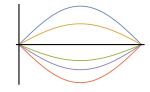
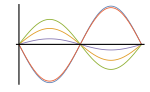
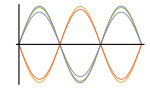
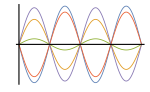

```mathematica
Table[Show[Plot[Table[asol[x,t][[m]],{t,0,4}]//Evaluate,{x,0,Pi},Ticks->False,PlotStyle->{Thickness[0.004]},ImageSize->150]],{m,4}]
```

5 - 13 Deflection of the String
Find u(x,t) for the string of length L=1 and c^2=1 when the initial velocity is zero and the initial deflection with small k (say, 0.01) is as follows. Sketch or graph u(x,t) as in Fig. 291 in the text.

5. k sin 3πx

```mathematica
Clear["Global`*"]
```

```mathematica
weqn=D[u[x,t],{t,2}]==D[u[x,t],{x,2}]
```

u^(0,2)[x,t]==u^(2,0)[x,t]

```mathematica
bc={u[0,t]==0,u[1,t]==0}
```

{u[0,t]==0,u[1,t]==0}

```mathematica
ic = {u[x, 0] == ( k Sin[3 π x]) ,Derivative[0,1][u][x, 0] == 0}
```

{u[x,0]==k Sin[3 π x],u^(0,1)[x,0]==0}

```mathematica
dsol=FullSimplify[DSolve[{weqn,bc,ic},u,{x,t}]]
```

{{u→Function[{x,t},k Cos[3 π t] Sin[3 π x]]}}

After some slight tinkering, Mathematica came through with text answer. I think the FullSimplify definitely helped.

7. kx(1-x)

```mathematica
Clear["Global`*"]
```

```mathematica
weqn=D[u[x,t],{t,2}]==D[u[x,t],{x,2}]
```

u^(0,2)[x,t]==u^(2,0)[x,t]

```mathematica
bc={u[0,t]==0,u[1,t]==0}
```

{u[0,t]==0,u[1,t]==0}

```mathematica
ic = {u[x, 0] == (k x)(1-x) ,Derivative[0,1][u][x, 0] == 0}
```

{u[x,0]==k (1-x) x,u^(0,1)[x,0]==0}

```mathematica
dsol=FullSimplify[DSolve[{weqn,bc,ic},u,{x,t}]]
```

{{u→Function[{x,t},-(4 (-1+(-1)^K[1]) k Cos[π t K[1]] Sin[π x K[1]])/(π^3 K[1]^3)K[1]1∞]}}

```mathematica
dsol2 =Simplify[dsol/.K[1]->m]
```

{{u→Function[{x,t},-(4 (-1+(-1)^m) k Cos[π t m] Sin[π x m])/(π^3 m^3)m1∞]}}

The green cell above matches the text’s answer.

9. Piecewise[{{x/5, 0<x<1/2}, {2/10-x/5, 1/2<x<1}}]

```mathematica
rat=Piecewise[{{x/5, 0<x<1/2}, {2/10-x/5, 1/2<x<1}}];
```

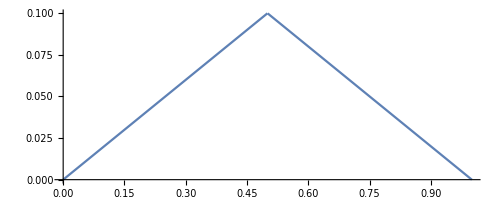

```mathematica
Plot[rat,{x,0,1},AspectRatio->Automatic]
```

I believe the below series of cells is set up correctly; however, in the brown cell below, Mathematica declines to calculate the answer. (From hints in StackExchange, I put all derivative forms on one side of equals sign in weqn.)

```mathematica
Clear["Global`*"]
```

```mathematica
weqn=D[u[x,t],{t,2}]-D[u[x,t],{x,2}]==0
```

u^(0,2)[x,t]-u^(2,0)[x,t]==0

```mathematica
bc={u[0,t]==0,u[el,t]==0}
```

{u[0,t]==0,u[el,t]==0}

```mathematica
(*ic = u[x, 0] =={ Piecewise[{{x/5,0<x<1/2},{1/5-x/5,1/2<x<1}} ],u^(0,1)[x, 0] == 0}*)
```

```mathematica
ic = u[x, 0] =={ Piecewise[{{(2 k)/eL x,0<x<eL/2},{(2 k)/eL(eL-x),eL/2<x<eL}} ],Derivative[0,1][u][x, 0] == 0}
```

u[x,0]=={Piecewise[{{(2 k x)/eL, 0<x<eL/2}, {(2 k (eL-x))/eL, eL/2<x<eL}, {0, True}}],u^(0,1)[x,0]==0}

```mathematica
dsol=FullSimplify[DSolve[{weqn,bc,ic},u,{x,t}]]
```

DSolve[{u^(0,2)[x,t]==u^(2,0)[x,t],{u[0,t]==0,u[1,t]==0},u[x,0]=={Piecewise[{{(2 k x)/eL, 0<x<eL/2}, {(2 k (eL-x))/eL, eL/2<x<eL}, {0, True}}],u^(0,1)[x,0]==0}},u,{x,t}]

So I have to conclude that this approach only works with relatively simple deflection equations. For a successful alternate approach, see problem 11.

Example 1 on p. 550 gives an exact template of the answer and its necessary expression:
u(x,t)=(8k)/π^2[1/1^2 sin(π/L x)cos(πc/L)t-1/3^2 sin((3π)/L x)cos((3πc)/L)t+1/5^2 sin((5π)/L x)cos((5πc)/L)t-⋯], or, in this case,

0.8/π^2(cos πt sin πx - 1/9 cos 3πt sin 3πx + 1/25 cos 5πt sin 5πx - ⋯)

11. Piecewise[{{0, 0<x<1/4}, {x-1/4, 1/4<x<1/2}, {3/4-x, 1/2<x<3/4}, {0, 3/4<x<1}}]

This problem has a more challenging form. I found a very effective solution procedure at http://math.iit.edu/~fass/461_handouts.html

```mathematica
Clear["Global`*"]
```

Solve the wave equation with the following parameters and initial displacement:

```mathematica
c=1;L=1;h=0.25;f[x_]:=Piecewise[{{0,0<x<L/4},{-L/4+ x,L/4<x<L/2},{(3 L)/4 -x,L/2<x<(3 L)/4},{0,(3 L)/4<x<L}}];
```

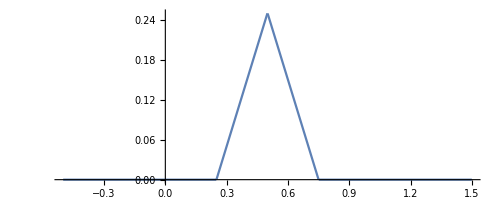

```mathematica
Plot[f[x],{x,-L/2,(3L)/2},AspectRatio->Automatic, PlotRange->Full]
```

Compute the Fourier coefficients. Since the initial velocity g(x)=0,  B_n=0 and

```mathematica
A[n_] = (2/L) Integrate[f[x]Sin[n Pi x/L],{x,0,L}]
```

(2 (-Sin[(n π)/4]+2 Sin[(n π)/2]-Sin[(3 n π)/4]))/(n^2 π^2)

with eigenvalues

```mathematica
Lambda[n_]=((c n Pi)/L)^2
```

n^2 π^2

The n-th partial sum of the Fourier series solution of the wave equation is

```mathematica
u[x_,t_,N_]:=Sum[A[n] Cos[Sqrt[Lambda[n]]t]Sin[n Pi x/L],{n,1,N}]
```

Give the partial sum approximation in a general form.

```mathematica
u[x,t,6]
```

(2 (2-√2) Cos[π t] Sin[π x])/π^2+(2 (-2-√2) Cos[3 π t] Sin[3 π x])/(9 π^2)+(2 (2+√2) Cos[5 π t] Sin[5 π x])/(25 π^2)

The green cell above matches the answer in the text.

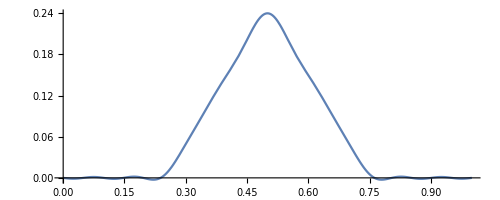

```mathematica
Plot[u[x,0,20],{x,0,L},AspectRatio->Automatic]
```

13. Piecewise[{{2x-4 x^2, 0<x<1/2}, {0, 1/2<x<1}}]

Repeating the procedure used in problem 11,

```mathematica
Clear["Global`*"]
```

Solve the wave equation with the following parameters and initial displacement:

```mathematica
c=1;L=1;h=0.25;f[x_]:=Piecewise[{{2 x-4 x^2,0<x<L/2},{0,L/2<x<L}}];
```

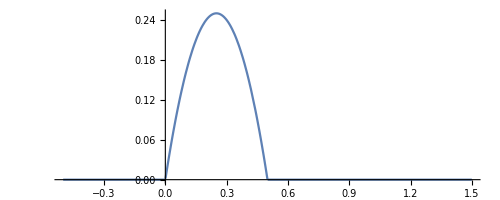

```mathematica
Plot[f[x],{x,-L/2,(3L)/2},AspectRatio->Automatic, PlotRange->Full]
```

Compute the Fourier coefficients. Since the initial velocity g(x)=0,  B_n=0 and

```mathematica
A[n_] = (2/L) Integrate[f[x]Sin[n Pi x/L],{x,0,L}]
```

-(4 (-4+4 Cos[(n π)/2]+n π Sin[(n π)/2]))/(n^3 π^3)

with eigenvalues

```mathematica
Lambda[n_]=((c n Pi)/L)^2
```

n^2 π^2

The n-th partial sum of the Fourier series solution of the wave equation is

```mathematica
u[x_,t_,N_]:=Sum[A[n] Cos[Sqrt[Lambda[n]]t]Sin[n Pi x/L],{n,1,N}]
```

Give the partial sum approximation in a general form.

```mathematica
u[x,t,6]
```

-(4 (-4+π) Cos[π t] Sin[π x])/π^3+(4 Cos[2 π t] Sin[2 π x])/π^3-(4 (-4-3 π) Cos[3 π t] Sin[3 π x])/(27 π^3)-(4 (-4+5 π) Cos[5 π t] Sin[5 π x])/(125 π^3)+(4 Cos[6 π t] Sin[6 π x])/(27 π^3)

The green cell above matches the answer in the text.

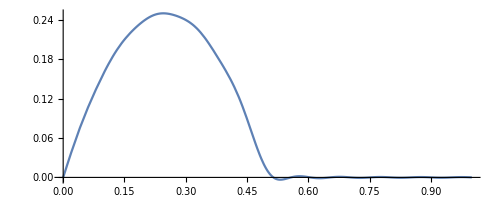

```mathematica
Plot[u[x,0,20],{x,0,L},AspectRatio->Automatic]
```

15 - 20 Separation of a Fourth-Order PDE. Vibrating Beam
By the principles used in modeling the string it can be shown that small free vertical vibrations of a uniform elastic beam (Fig. 292) are modeled by the fourth-order PDE
(21)    (∂_2 u)/(∂_2 t)=-c^2(∂_4 u)/(∂_4 x)
where c^2=EIρA  (E=Young’s modulus of elasticity, I=moment of inertia of the cross section with repsect to the y-axis in the figure, ρ=density, A=cross-sectional area).

Judging by the performance in the last section, I’m not even going to try to get Mathematica to solve equations of

15. Substituting u=F(x)G(t) into (21), show that F^(4)/F=-(G̈)/(c^2 G)=const.